```mathematica
Clear[H,A,B,x1,x0,psi,out,Dmat,d1,d2,d3,d4,psi0,U,Re0,Re1,Im1,Im0]
Clear[sigX,sigZ,sigY,theta1,theta2,theta3,alpha]


A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];

sigX = PauliMatrix[1];
sigY = PauliMatrix[2];
sigZ = PauliMatrix[3];

(*rz[theta_] = Exp[-I*theta*sigZ/2];*)
rz[theta_] = Cos[theta/2]*IdentityMatrix[2] - I*Sin[theta/2]*sigZ;
rx[theta_] =Cos[theta/2]*IdentityMatrix[2] - I*Sin[theta/2]*sigX;

Print["Rotation U:"]
buildU[alpha_,theta1_,theta2_,theta3_]:= Exp[I*alpha]*rz[theta1].rx[theta2].rz[theta3];
U = buildU[alpha,theta1,theta2,theta3];
Print[MatrixForm[U]]
(*A = IdentityMatrix[2];
B= IdentityMatrix[2];*)

(*U = {{u1,u2},{u3,u4}};*)

H = 1/(Sqrt[2])*{{1,1},{1,-1}};
Print["Eqs:"]
eqs = Thread[Flatten/@(U==H)]
Print["Sovling for rotation angles"]
sol = Solve[eqs,{alpha,theta1,theta2,theta3}];
Normal[sol] /.{C[1]->1,C[2]->1,C[3]->1,C[4]->1}
```

Rotation U:

(ⅇ^(ⅈ alpha) Cos[theta2/2] (Cos[theta1/2]-ⅈ Sin[theta1/2]) (Cos[theta3/2]-ⅈ Sin[theta3/2]) | -ⅈ ⅇ^(ⅈ alpha) (Cos[theta1/2]-ⅈ Sin[theta1/2]) Sin[theta2/2] (Cos[theta3/2]+ⅈ Sin[theta3/2])
-ⅈ ⅇ^(ⅈ alpha) (Cos[theta1/2]+ⅈ Sin[theta1/2]) Sin[theta2/2] (Cos[theta3/2]-ⅈ Sin[theta3/2]) | ⅇ^(ⅈ alpha) Cos[theta2/2] (Cos[theta1/2]+ⅈ Sin[theta1/2]) (Cos[theta3/2]+ⅈ Sin[theta3/2]))

Eqs:

{ⅇ^(ⅈ alpha) Cos[theta2/2] (Cos[theta1/2]-ⅈ Sin[theta1/2]) (Cos[theta3/2]-ⅈ Sin[theta3/2])==1/(√2),-ⅈ ⅇ^(ⅈ alpha) (Cos[theta1/2]-ⅈ Sin[theta1/2]) Sin[theta2/2] (Cos[theta3/2]+ⅈ Sin[theta3/2])==1/(√2),-ⅈ ⅇ^(ⅈ alpha) (Cos[theta1/2]+ⅈ Sin[theta1/2]) Sin[theta2/2] (Cos[theta3/2]-ⅈ Sin[theta3/2])==1/(√2),ⅇ^(ⅈ alpha) Cos[theta2/2] (Cos[theta1/2]+ⅈ Sin[theta1/2]) (Cos[theta3/2]+ⅈ Sin[theta3/2])==-1/(√2)}

Sovling for rotation angles

{{alpha→(3 π)/2,theta1→(5 π)/2,theta2→(5 π)/2,theta3→(5 π)/2},{alpha→(3 π)/2,theta1→(5 π)/2,theta2→(9 π)/2,theta3→(9 π)/2},{alpha→(3 π)/2,theta1→(7 π)/2,theta2→(7 π)/2,theta3→(7 π)/2},{alpha→(3 π)/2,theta1→(7 π)/2,theta2→(11 π)/2,theta3→(11 π)/2},{alpha→(3 π)/2,theta1→(9 π)/2,theta2→(5 π)/2,theta3→(9 π)/2},{alpha→(3 π)/2,theta1→(9 π)/2,theta2→(9 π)/2,theta3→(5 π)/2},{alpha→(3 π)/2,theta1→(11 π)/2,theta2→(7 π)/2,theta3→(11 π)/2},{alpha→(3 π)/2,theta1→(11 π)/2,theta2→(11 π)/2,theta3→(7 π)/2},{alpha→(5 π)/2,theta1→(5 π)/2,theta2→(5 π)/2,theta3→(9 π)/2},{alpha→(5 π)/2,theta1→(5 π)/2,theta2→(9 π)/2,theta3→(5 π)/2},{alpha→(5 π)/2,theta1→(7 π)/2,theta2→(7 π)/2,theta3→(11 π)/2},{alpha→(5 π)/2,theta1→(7 π)/2,theta2→(11 π)/2,theta3→(7 π)/2},{alpha→(5 π)/2,theta1→(9 π)/2,theta2→(5 π)/2,theta3→(5 π)/2},{alpha→(5 π)/2,theta1→(9 π)/2,theta2→(9 π)/2,theta3→(9 π)/2},{alpha→(5 π)/2,theta1→(11 π)/2,theta2→(7 π)/2,theta3→(7 π)/2},{alpha→(5 π)/2,theta1→(11 π)/2,theta2→(11 π)/2,theta3→(11 π)/2}}

```mathematica
U =H;
Dmat= DiagonalMatrix[{d1,d2,d3,d4}];

x0 = 1/Sqrt[2];
x1= -1/Sqrt[2];

psi0 ={x0,0,x1,0};

"A tensor H";
AtH= ArrayFlatten[TensorProduct[A,U]];
"H tensor B";
HtB = ArrayFlatten[TensorProduct[U,B]];

"HtB D AtH";
finalMat = Simplify[HtB.Dmat.AtH];

"Final Product";
phi =( finalMat.psi0)[[{1,2}]]//Normalize//Simplify;
"No Gadget:";
psi = B.H.A.{x0,x1};
```

```mathematica
Print["Minimizations"]
Re0 = Abs[Re[psi[[1]]] - Re[phi[[1]]]]^2;
Re1 = Abs[Re[psi[[2]]] - Re[phi[[2]]]]^2; 
Im0 = Abs[(Im[psi[[1]]] - Im[phi[[1]]])]^2; 
Im1 = Abs[(Im[psi[[2]]]-  Im[phi[[2]]])]^2;

t = {0,0,0,0};
For[i = 0,i < 100,i++,t = t + NArgMin[Re0 + Re1 + Im0 + Im1,{d1,d2,d3,d4}]]


t = t/Mean[Abs[t]];
Print["Value of t:" ]
Print[t]

Dmat2 = DiagonalMatrix[t];
newFinal =  Simplify[HtB.Dmat2.AtH];
phi2 = ( newFinal.psi0)[[{1,2}]]//Normalize//Simplify;

printer = Abs[{phi2[[1]],phi2[[2]],psi[[1]],psi[[2]]}]^2;

Print["phi 2:"]
Print[phi2]
Print["OG"]
Print[psi]
Print["overlap:"]
Print[prod[phi2,psi]]
Print[printer]
listEQ = {Re0,Re1,Im0,Im1};
```

Minimizations

Value of t:

{1.,1.,1.,-1.}

phi 2:

{0.0242225-0.0972896 ⅈ,0.864086-0.493258 ⅈ}

OG

{0.0242225-0.0972897 ⅈ,0.864086-0.493258 ⅈ}

overlap:

prod[{0.0242225-0.0972896 ⅈ,0.864086-0.493258 ⅈ},{0.0242225-0.0972897 ⅈ,0.864086-0.493258 ⅈ}]

{0.010052,0.989948,0.010052,0.989948}

```mathematica
getArgMins[psi_,phi_,params_]:= Module[{Re0,Re1,Im0,Im1},
Re0 = Abs[Re[psi[[1]]] - Re[phi[[1]]]]^2;
Re1 = Abs[Re[psi[[2]]] - Re[phi[[2]]]]^2; 
Im0 = Abs[(Im[psi[[1]]] - Im[phi[[1]]])]^2; 
Im1 = Abs[(Im[psi[[2]]]-  Im[phi[[2]]])]^2;
Return[NArgMin[Re0+Re1+Im0+Im1,params]]
]
```

```mathematica
getAverageOverlap[alpha_,theta1_,theta2_,theta3_]:= Module[{A,B,psi,psi0,t,AtU,UtB,Dmat,d1,d2 ,d3,d4,finalMat,phi,temp,tot,U,n},
n = 10;
t = {0,0,0,0};
U = buildU[alpha,theta1,theta2,theta3];
For[i=0,i<n,i++,
(*Print[StringForm["First For Loop: ``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[U,B]];
Dmat = DiagonalMatrix[{d1,d2,d3,d4}];
finalMat = UtB.Dmat.AtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
temp = getArgMins[psi,phi,{d1,d2,d3,d4}];
t = t +temp  ;
(*Print[StringForm["Output temp: ``",temp]];*)
];
(*Print[StringForm["Average t: ``",t/n]];*)
t = t/Mean[Abs[t]];
(*Print[StringForm["Final t: ``",t]];*)
Dmat = DiagonalMatrix[t];
tot = 0;

For[i=0,i<n,i++,
(*Print[StringForm["Second For Loop:``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[U,B]];
finalMat = UtB.Dmat.AtU;
phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
tot =tot + prod[phi,psi];
];
(*Print[StringForm["Final Average Overlap: ``",tot/n]];*)
Return[Abs[tot/n]]
]

getAvgOverlapList[list_]:=getAverageOverlap[list[[1]],list[[2]],list[[3]],list[[4]]]
(*tab=Table[NMaximize[getAverageOverlap[a,i,j,b],{a,b}],{i,-Pi/2,Pi/2,0.1},{j,-Pi/2,Pi/2,0.1}]*)
```

```mathematica
1.6*(4Pi/0.5)^2
%/60
```

1010.65

16.8441

```mathematica
Clear[i,j,h]
(1.6/3600)*(4*32)^2
Export["data.csv",newTab]
```

7.28178

data.csv

```mathematica
h[a_] := getAverageOverlap[Pi/2,a[[1]],a[[2]],Pi/2]
tab0 =  Table[{i,j},{i,0,4Pi,Pi/32},{j,0,4Pi,Pi/32}]
tab0 = Flatten[tab0,1]
newTab = Map[h,tab0]
Export["data.csv",newTab]
plotter = Table[Append[tab0[[i]],newTab[[i]]],{i,1,Length[newTab]}]
Export["plotter.csv",plotter]
```

{{{0,0},{0,π/32},{0,π/16},{0,(3 π)/32},{0,π/8},{0,(5 π)/32},{0,(3 π)/16},{0,(7 π)/32},{0,π/4},{0,(9 π)/32},{0,(5 π)/16},{0,(11 π)/32},{0,(3 π)/8},{0,(13 π)/32},{0,(7 π)/16},{0,(15 π)/32},{0,π/2},96,{0,(113 π)/32},{0,(57 π)/16},{0,(115 π)/32},{0,(29 π)/8},{0,(117 π)/32},{0,(59 π)/16},{0,(119 π)/32},{0,(15 π)/4},{0,(121 π)/32},{0,(61 π)/16},{0,(123 π)/32},{0,(31 π)/8},{0,(125 π)/32},{0,(63 π)/16},{0,(127 π)/32},{0,4 π}},127,{{4 π,0},127,{1}}}
 |  |  |  |

{{0,0},{0,π/32},{0,π/16},{0,(3 π)/32},{0,π/8},{0,(5 π)/32},{0,(3 π)/16},{0,(7 π)/32},{0,π/4},{0,(9 π)/32},{0,(5 π)/16},{0,(11 π)/32},{0,(3 π)/8},{0,(13 π)/32},{0,(7 π)/16},{0,(15 π)/32},16610,{4 π,(57 π)/16},{4 π,(115 π)/32},{4 π,(29 π)/8},{4 π,(117 π)/32},{4 π,(59 π)/16},{4 π,(119 π)/32},{4 π,(15 π)/4},{4 π,(121 π)/32},{4 π,(61 π)/16},{4 π,(123 π)/32},{4 π,(31 π)/8},{4 π,(125 π)/32},{4 π,(63 π)/16},{4 π,(127 π)/32},{4 π,4 π}}
 |  |  |  |

NArgMin::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NArgMin::cvmit will be suppressed during this calculation.

{0.537558,0.739141,0.472794,0.434032,0.695546,0.334638,0.520532,0.69503,0.494819,16623,0.731562,0.321969,0.545326,0.578236,0.554089,0.6246,0.340586,0.57249,0.591681}
 |  |  |  |

data.csv

{{0,0,0.537558},{0,π/32,0.739141},{0,π/16,0.472794},{0,(3 π)/32,0.434032},{0,π/8,0.695546},{0,(5 π)/32,0.334638},16630,{4 π,(31 π)/8,0.554089},{4 π,(125 π)/32,0.6246},{4 π,(63 π)/16,0.340586},{4 π,(127 π)/32,0.57249},{4 π,4 π,0.591681}}
 |  |  |  |

plotter.csv

7.85398

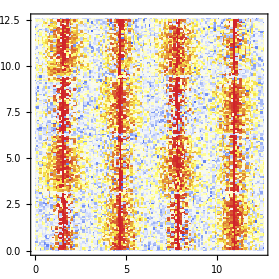

-Graphics3D-

```mathematica
newTab;
5Pi/2 //N
plotter = Table[Append[tab0[[i]],newTab[[i]]],{i,1,Length[newTab]}];
ListDensityPlot[plotter,InterpolationOrder->0,ColorFunction->"TemperatureMap"]
ListPlot3D[plotter,InterpolationOrder->3]
```

```mathematica
constructPhi[alpha_,beta_,Unitary_,D_]:= Module[{psi,A,B,AtU,UtB,finalMat,phi},
psi  = {alpha,0,beta,0}//Normalize;
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
AtU = ArrayFlatten[TensorProduct[A,Unitary]];
UtB = ArrayFlatten[TensorProduct[Unitary,B]];
finalMat =  Simplify[UtB.D.AtU];
phi = ( finalMat.psi0)[[{1,2}]]//Normalize//Simplify;
Return[phi];
]
```

```mathematica
Clear[t,m1,m2,m3,m4]
prod[psi_,phi_]:=( psi.Conjugate[phi])*(phi.Conjugate[psi])
f[AtU_,UtB_,d1_,d2_,d3_,d4_]:= Module[{Dmat,phi,Re0,Re1,Im0,Im1},
Dmat = DiagonalMatrix[{d1,d2,d3,d4}];
phi = (UtB.Dmat.AtU.psi0);
phi = phi[[1;;2]]//Normalize//Simplify;
Re0 = (Re[psi[[1]]] - Re[phi[[1]]])^2;
Re1 = (Re[psi[[2]]] - Re[phi[[2]]])^2;

Im0 = (Im[psi[[1]]] - Im[phi[[1]]])^2;
Im1 = (Im[psi[[2]]] - Im[phi[[2]]])^2;
Sum[i,{i,{Re0,Re1,Im0,Im1}}]
]

g[d1_,d2_,d3_,d4_]:=f[AtH,HtB,d1,d2,d3,d4]
"testing g"
Minimize[f[AtH,HtB,m1,m2,m3,m4],{m1,m2,m3,m4}]
```

testing g

{2.07073×10^-15,{m1→0.40031,m2→0.40031,m3→0.40031,m4→-0.40031}}

```mathematica
{{1,0},{0,-1}}.{{0,1},{1,0}}
```

{{0,1},{-1,0}}